# Experiments for distribution estimation for probabilistic max-finder

## Introduction

Seeing the good theoretical performance of local-maximum finding, I wanted to investigate the possibility of just doing a local-max finder from a Bayesian perspective.

Some notation. x_i=a_i+ξ_i where a_i is the original value of the sum of Lorentzians at that point and ξ_i is iid noise.Since we know that most of the noise we care about is white - Gaussian, this is what I will use in my experiments.

To find a local maximum (ignoring the continuous nature of the underlying functions), we want to find where a_(i-1)<a_i<a_(i+1).  Note that this is composed of two parts Subscript[a, i-1]<Subscript[a, i] and Subscript[a, i]<Subscript[a, i+1].  These parts are not independent.  In fact, it is much more likely that they are both true or both false than that there is a local maximum.

## Preliminary setup

l is the Lorentzian function/Cauchy PDF as defined in Paul Anderson' s thesis.This makes γ the width at half - height, amp the amplitude of the mode, and x0 the location of the mode on the x axis.

```mathematica
l[x_,amp_,γ_,x0_]:=amp γ^2/(4 (x-x0)^2+γ^2)
```

## Distribution of order stats

Note: I never got to actually looking at the distribution of P(a_(i-1)<a_i|x_(i-1),x_i,a_i<a_(i+1)) which is what I really need to do appropriate inference

### For one peak

onePeakSamples returns numSamp samples of

P(a_(i-1)<a_i,a_i<a_(i+1),x_(i-1),x_i,x_(i+1)| discretizationInterval,truncationWidth,noiseStd,amp,γ)

for a single Lorentzian. Since I will be choosing samples randomly, I decided to set x0 to 0. amp and γ are the amplitude and width-at-half-height.  Truncation width is the width of the interval around the origin where the discretization takes place.  discretization interval is the interval on the independent axis between adjacent Subscript[a, i].  noiseStd is the standard-deviation of the Gaussian from which the noise is chosen.

```mathematica
onePeakSamples[numSamp_, truncationWidth_,discretizationInterval_,noiseStd_,amp_,γ_]:=
With[{δ=discretizationInterval,σ=noiseStd,ww=truncationWidth/2},
(*hidParams are the coordinates+noise for each sample*)
With[{hidParams=Table[Join[{RandomReal[{-ww,ww}]},Table[RandomReal[NormalDistribution[0,σ]],{3}]],{numSamp}]},
Map[With[{i0=#[[1]],n0=#[[2]],n1=#[[3]],n2=#[[4]]},
With[{a0=l[i0,amp,γ,0],a1=l[i0+δ,amp,γ,0],a2=l[i0+2δ,amp,γ,0]},
{a0<a1,a1<a2,a0+n0,a1+n1,a2+n2}
]]&,hidParams]
]]
```

This is a noise-free version

```mathematica
onePeakSamplesNoNoise[numSamp_, truncationWidth_,discretizationInterval_,amp_,γ_]:=
With[{δ=discretizationInterval,ww=truncationWidth/2},
(*hidParams are the coordinates+noise for each sample*)
With[{hidParams=Table[{RandomReal[{-ww,ww}]},{numSamp}]},
Map[With[{i0=#[[1]]},
With[{a0=l[i0,amp,γ,0],a1=l[i0+δ,amp,γ,0],a2=l[i0+2δ,amp,γ,0]},
{a0<a1,a1<a2,a0,a1,a2}
]]&,hidParams]
]]
```

#### Noisy samples l[x,1,1,0] 32 samp/unit noise=1%

Here we look at samples for one width 1, height 1 peak.  The sample distance is chosen so that there are 32 samples per unit and the noise is 1% of peak height.

```mathematica
Timing[rawSampW1H1N01=onePeakSamples[100000,6,1/32,1/100,1,1];]
```

{38.0972,Null}

Here we have all xy pairs where a_(i-1)<a_i

```mathematica
sampW1H1N01A=Map[{#[[3]],#[[4]]}&,Select[rawSampW1H1N01,#[[1]]&]]
```

{{0.0321098,0.0445074},{0.227837,0.239504},{0.189007,0.185476},«49860»,{0.060517,0.074792},{0.132986,0.151549}}

Prior probability  P(a_(i-1)<a_i)≈0.50

```mathematica
N[Length[sampW1H1N01A]/Length[rawSampW1H1N01]]
```

0.49865

And a histogram.  Showing P(x_(i-1),x_i|a_(i-1)<a_i)

```mathematica
Histogram3D[sampW1H1N01A]
```

-Graphics3D-

We can rotate the data by 45 degrees to get better resolution (unrotated, we waste a lot of bins on the empty areas).  Those areas are empty because the derivative is not sharp enough to give those combinations at our discretization interval.

```mathematica
sampW1H1N01ARot=Map[With[{x=#[[1]],y=#[[2]]},{x-y,x+y}/Sqrt[2]]&,sampW1H1N01A];
```

Here is the histogram.  The cross-section is the distribution of x-y and x+y=k   It looks Gaussian, which is to be expected.  The curve in the mode was unexpected.  But I think that is mainly because I didn't think things through enough.  The large number of samples near x+y=0 is because most samples will come from the area where the lorentzian has low magnitude.  (I need to think about this more). When it has low magnitude, it also has low slope.  This means that |a_i-a_(i-1)| is small so  a_(i-1)<a_i has little effect on how often such samples are chosen.  But, when |a_i-a_(i-1)| is large (near the origin, but not at it).

The process of creating a sample in this histogram can be looked at as: (1) choose an α<0 (this ensures that l[α-δ]<l[α]). (2) choose two Gaussian noise points u,v.  (3) plot (l[α-δ]+u,l[α]+v) (after rotation)

The x-y coordinate can be looked at as being l[α-δ]+u-l[α]-v=l[α-δ]-l[α]+u-v.  If δ is small, this can be looked at as δ times an approximation of the derivative at α+noise since u-v will be Gaussian distributed.

The x+y coordinate can be looked at as being  l[α-δ]+u+l[α]+v=l[α-δ]+l[α]+v+u.  If δ is small then l[α-δ]≈l[α].  So, we can regard it as 2 l[α]+noise.  u+v will be Gaussian distributed.

So, noise free, we would be plotting a scaled version of (dl[x]/dx@α,l[α])

Looking at the noise-fee version, below, it is almost identical to the noisy version.  Thus the noise I used was not enough to make a real difference.

```mathematica
Histogram3D[sampW1H1N01ARot]
```

-Graphics3D-

Here is the distribution of the x+y axis (skipping the beginning since it is much higher).  It should be proportional to the interval for which the lorentzian has a given height.

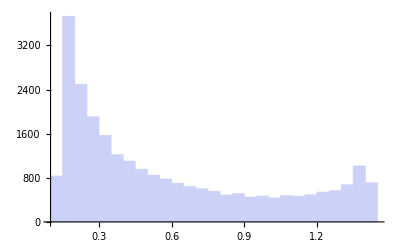

```mathematica
Histogram[Map[#[[2]]&,Select[sampW1H1N01ARot,0.2/Sqrt[2]<#[[2]]&]]]
```

Below, I look at the interval at which the Lorentzian has a given height.  There is some similarity to the sampled experiment.  But they are not identical.  (The noiseless version looks the same.)

```mathematica
Reduce[{l[x,1,1,0]==y, x< 0},x,Reals]
```

0<y<1&&x==-1/2 √((1-y)/y)

```mathematica
lInv[y_]:=-1/2 √((1-y)/y)
```

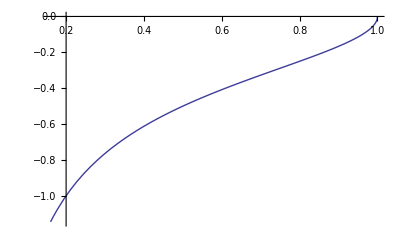

```mathematica
Plot[lInv[x],{x,0.16,1}]
```

```mathematica
lengthLorAtHeight[h_,δ_]:=Abs[lInv[h+δ]-lInv[h]]
```

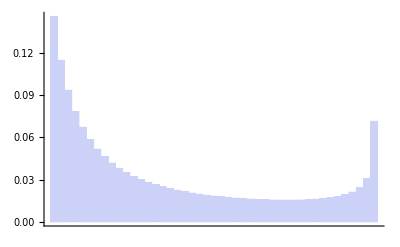

```mathematica
BarChart[Table[lengthLorAtHeight[h,0.02],{h,0.1,0.98,0.02}]]
```

This is similar to the derivative of the inverse

```mathematica
D[lInv[x],x]
```

-(-(1-x)/x^2-1/x)/(4 √((1-x)/x))

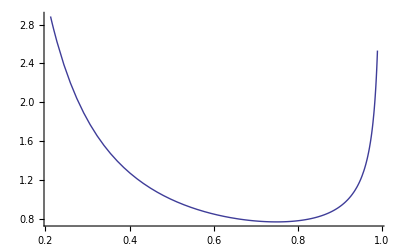

```mathematica
Bar[-(-(1-x)/x^2-1/x)/(4 √((1-x)/x)),{x,0.3/Sqrt[2],1.4/Sqrt[2]},AxesOrigin->{0,0},PlotRange->All]
```

Here is a slice from the middle

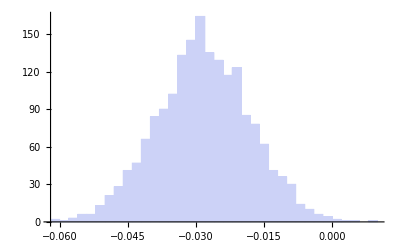

```mathematica
Histogram[Map[#[[1]]&,Select[sampW1H1N01ARot,0.9<#[[2]]<1.1&]]]
```

And one from the end

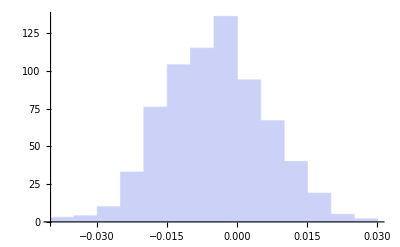

```mathematica
Histogram[Map[#[[1]]&,Select[sampW1H1N01ARot,1.4<#[[2]]&]]]
```

Here we have all xy pairs where a_(i-1)<a_i<a_(i+1)

```mathematica
sampW1H1N01Up=Map[{#[[3]],#[[4]]}&,Select[rawSampW1H1N01,#[[1]]&&#[[2]]&]];
```

```mathematica
Length[sampW1H1N01A]
```

49865

#### Noisy samples l[x,1,1,0] 32 samp/unit noise=0

```mathematica
Timing[rawSampW1H1N00=onePeakSamplesNoNoise[100000,6,1/32,1,1];]
```

{5.52716,Null}

```mathematica
sampW1H1N00A=Map[{#[[3]],#[[4]]}&,Select[rawSampW1H1N01,#[[1]]&]];
```

```mathematica
sampW1H1N00ARot=Map[With[{x=#[[1]],y=#[[2]]},{x-y,x+y}/Sqrt[2]]&,sampW1H1N00A];
```

```mathematica
Histogram3D[sampW1H1N00ARot]
```

-Graphics3D-

## How good of a criterion is the discrete local maximum

### For one peak

#### What answers does it produce when a_i is a peak

Look at when a_i is the closest point to a peak and the criterion is true.  That is when -δ/2<i<δ/2 where δ is the sampling interval and a_(i-1)<a_i<a_(i+1).

```mathematica
With[{a0=l[i-δ,1,1,0],a1=l[i,1,1,0],a2=l[i+δ,1,1,0]},Reduce[a0<a1&&a1>a2&&Abs[i]<δ/2,{i},Reals]
]
```

δ>0&&-δ/2<i<δ/2

It always produces the correct answer when a_i is a peak.

#### When is it true but a_i is not a peak

This is almost the same as the last but with the interval reversed

```mathematica
With[{a0=l[i-δ,1,1,0],a1=l[i,1,1,0],a2=l[i+δ,1,1,0]},Reduce[a0<a1&&a1>a2&&Abs[i]>δ/2&&δ>0,{i},Reals]
]
```

False

It never produces a false-positive result.